```mathematica
p=4Pi(10)^3(1.5-1)/(1.5+2(1));
```

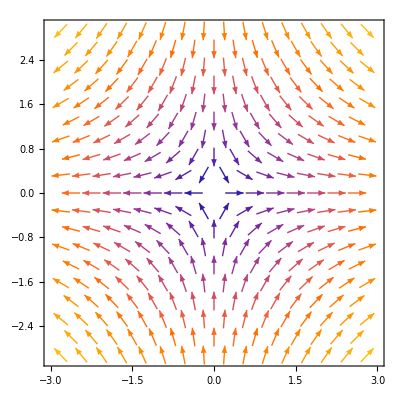

```mathematica
VectorPlot[{x,-y},{x,-3,3},{y,-3,3}]
```

```mathematica
(* Define the electric field in spherical coordinates *)
EFieldSpherical[r_, θ_, ϕ_] := {2 p Cos[θ]/(4Pi(1)^2*2^2),  p Sin[θ]/(4Pi(1)^2*2^2), 0} (* Example: Radial field *)

(* Convert to Cartesian coordinates *)
EFieldCartesian[x_, y_, z_] := Module[
  {r, θ, ϕ, Er, Eθ, Eϕ, Ex, Ey, Ez},
  
  (* Spherical to Cartesian transformation *)
  r = Sqrt[x^2 + y^2 + z^2];
  θ = ArcCos[z/r];
  ϕ = ArcTan[x, y];
  
  (* Extract spherical components *)
  {Er, Eθ, Eϕ} = EFieldSpherical[r, θ, ϕ];
  
  (* Convert components to Cartesian *)
  Ex = Er Sin[θ] Cos[ϕ] + Eθ Cos[θ] Cos[ϕ] - Eϕ Sin[ϕ];
  Ey = Er Sin[θ] Sin[ϕ] + Eθ Cos[θ] Sin[ϕ] + Eϕ Cos[ϕ];
  Ez = Er Cos[θ] - Eθ Sin[θ];
  
  {Ex, Ey, Ez}
]

(* Plot the field using VectorPlot3D *)
VectorPlot3D[
  EFieldCartesian[x, y, z], 
  {x, -10, 10}, {y,-10, 10}, {z,-10, 10},
  VectorScale -> Automatic, VectorPoints -> 10
]
```

-Graphics3D-

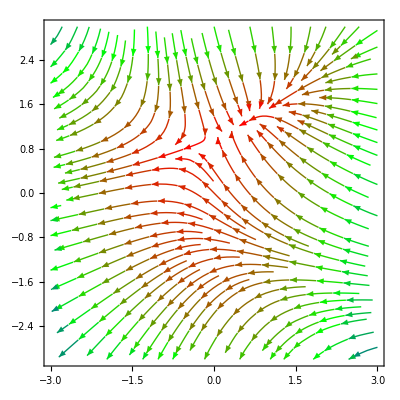

```mathematica
StreamPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3},StreamColorFunction->(Blend[{Red,Green,Blue},#5]&)]
```

```mathematica
dipole=StreamPlot3D[
  EFieldCartesian[x, y, z], 
  {x, -50, 50}, {y, -50, 50}, {z,-50, 50},Boxed->False,(*Removes the box*)Axes->False ]
```

-Graphics3D-

```mathematica
Export["Dipole.svg",dipole]
```

Dipole.svg